```mathematica
Remove["Global`*"]
```

Remove::rmnsm: There are no symbols matching "Global`*".

```mathematica
$Assumptions={n,m,nd,md,nd1,kd,kd1,nn}∈Integers ∧n≥ 0 ∧ m≥0∧nn>0
```

(n|m|nd|md|nd1|kd|kd1|nn)∈Integers&&n≥0&&m≥0&&nn>0

# Mathematica for Engineering Systems: Part II

## Introduction

Part II continues with Fourier Transforms, first continuous-time and second discrete-time Fourier Transform.

## Continuous-time systems

Fourier Transform (Continuous)

### Introduction

Mathematica has the flexibility to deal with various definitions of Fourier Transforms that are used in various disciplines. 
We use the definition that is common in signal processing. This option should be selected by adding an option in the arguments of the FourierTransform function: FourierParameters → {1,-1}.

### Fourier Transforms

#### problem 18.1.a

```mathematica
f1[t_]=Sin[ω0 t]
```

Sin[t ω0]

```mathematica
ft1[ω_]=FourierTransform[Sin[ω0 t],t,ω,FourierParameters->{1,-1}]
```

-ⅈ π DiracDelta[-ω+ω0]+ⅈ π DiracDelta[ω+ω0]

#### problem 18.1.b

```mathematica
f2[t_]=Piecewise[{{ⅇ^(-t/τ), t>0}, {0, True}}]
```

Piecewise[{{ⅇ^(-t/τ), t>0}, {0, True}}]

```mathematica
ft2[ω_]=FourierTransform[f2[t],t,ω,FourierParameters->{1,-1}]
```

-(ⅈ τ)/(-ⅈ+τ ω)

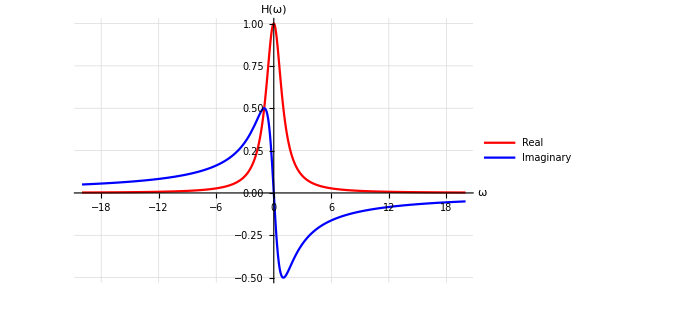

```mathematica
Plot[{Re[ft2[ω]/.τ->1],Im[ft2[ω]/.τ->1]},{ω,-20,20},PlotRange->Full,GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"ω","H(ω)"},PlotStyle->{Red,Blue},BaseStyle->12,PlotLegends->{"Real","Imaginary"}]
```

#### Additional

```mathematica
spec2[ω_]=FourierTransform[(HeavisideTheta[t+a]-HeavisideTheta[t-a]),t,ω]
```

(√(2/π) Sin[a ω])/ω

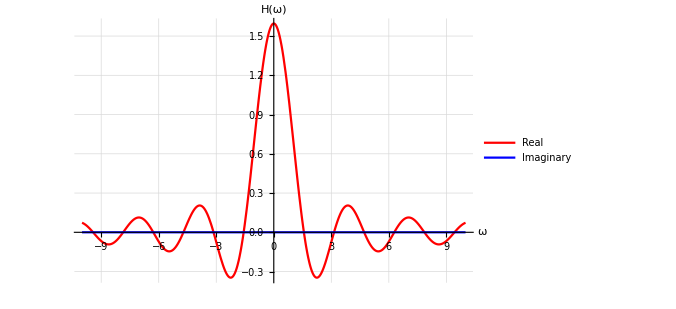

```mathematica
Plot[{Re[spec2[ω]/.a->2],Im[spec2[ω]/.a->2]},{ω,-10,10},PlotRange->Full,GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"ω","H(ω)"},PlotStyle->{Red,Blue},BaseStyle->12,PlotLegends->{"Real","Imaginary"}]
```

#### Problem 18.5.d (dynamic version)

In this example we explore the effect of the length of a finite-length cosine function in relation to its frequency on the Fourier spectrum. You can explore the effect by sliding the frequency and the pulse length.

First define the time function

```mathematica
f5d[t_]=Piecewise[{{Cos[ω0 t], -τ/2<t<τ/2}, {0, True}}]
```

Piecewise[{{Cos[t ω0], -τ/2<t<τ/2}, {0, True}}]

and take the Fourier Transform

```mathematica
f5dw[ω_]=FourierTransform[f5d[t],t,ω,FourierParameters->{1, -1}]
```

-(2 (ω Cos[(τ ω0)/2] Sin[(τ ω)/2]-ω0 Cos[(τ ω)/2] Sin[(τ ω0)/2]) (-1+UnitStep[-τ]))/(ω^2-ω0^2)

```mathematica
Manipulate[Grid[{{
Plot[f5d[t]/.{t0->1,ω0->ωd,τ->τd},{t,-5,5},PlotRange->Full,GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->300,AxesLabel->{"t","f(t)"},PlotStyle->Red,BaseStyle->12],
Plot[{Re[f5dw[ω]/.{t0->1,ω0->ωd,τ->τd}],Im[f5dw[ω]/.{t0->1,ω0->ωd,τ->τd}]},{ω,-40,40},PlotRange->Full,GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->300,AxesLabel->{"ω","F(ω)"},PlotStyle->{Red,Blue},BaseStyle->12,PlotLegends->{"Real","Imaginary"}]
}}],
{{τd,3,"Pulse length [s]"},1,10},{{ωd,5.3,"Frequency [rad/s]"},1,20}]
```

A few notes about your explorations: 
- The more cycles in the pulse, the sharper the frequency peaks.
- The time-signal is the product of a cosine function and a block-function, so the Fourier spectrum should be the convolution of two delta-peaks with a sinc-function.

### Inverse Fourier Transforms

#### Problem 18.2.a

```mathematica
fw1[ω_]=2 π DiracDelta[ω-ω0]
```

2 π DiracDelta[ω-ω0]

```mathematica
fw1t[t_]=InverseFourierTransform[fw1[ω],ω,t,FourierParameters->{1,-1}]
```

ⅇ^(ⅈ t ω0)

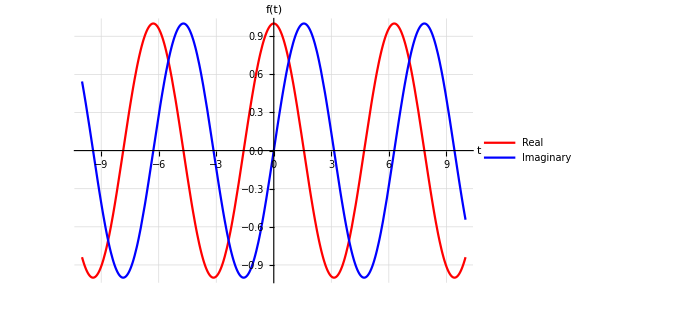

```mathematica
Plot[{Re[fw1t[t]/.ω0->1],Im[fw1t[t]/.ω0->1]},{t,-10,10},PlotRange->Full,GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"t","f(t)"},PlotStyle->{Red,Blue},BaseStyle->12,PlotLegends->{"Real","Imaginary"}]
```

### Convolution

#### Problem 18.6

Define two time functions:

```mathematica
g61[t_]=UnitStep[t] ⅇ^-t
```

ⅇ^-t UnitStep[t]

```mathematica
g62[t_]=UnitStep[t] ⅇ^(-2 t)
```

ⅇ^(-2 t) UnitStep[t]

Calculate the convolution of the two time functions to obtain a new time function.

```mathematica
g6t[t]=Convolve[g61[tt],g62[tt],tt,t]
```

ⅇ^(-2 t) (-1+ⅇ^t) UnitStep[t]

Calculate the Fourier Transform of the two original time functions and that of the convolution

```mathematica
g6tw[ω_]=FourierTransform[g6t[t],t,ω,FourierParameters->{1, -1}]
```

1/(2+3 ⅈ ω-ω^2)

```mathematica
g61w[ω_]=FourierTransform[g61[t],t,ω,FourierParameters->{1, -1}]
```

-ⅈ/(-ⅈ+ω)

```mathematica
g62w[ω_]=FourierTransform[g62[t],t,ω,FourierParameters->{1, -1}]
```

-ⅈ/(-2 ⅈ+ω)

A convolution in the time domain is a product in the Fourier domain, so we take the product of the first two transformed functions

```mathematica
g6wt[ω_]=g61w[ω] g62w[ω]
```

-1/((-ⅈ+ω) (-2 ⅈ+ω))

and compare it with the transform of the convoluted function

```mathematica
g6tw[ω]==g6wt[ω]//FullSimplify
```

True

Fourier Series

### Intro

Periodic-time signals form a special subset of all signals, since there is a lowest frequency in the frequency representation of the signal. This frequency is ω_0=(2 π)/T_0 with T_0 the period of the signal. The direct consequence is that for a frequency representation we only need the frequencies that are multiples of the lowest frequency. Let us demonstrate this on a square wave signal.

For a repetitive signal we only have to define the signal on one interval:

```mathematica
fr[t_]=Piecewise[{{1, -1/2≤t <0}, {0, t==0}, {-1, 0<t≤ 1/2}}]
```

Piecewise[{{1, -1/2≤t<0}, {0, t==0}, {-1, 0<t≤1/2}, {0, True}}]

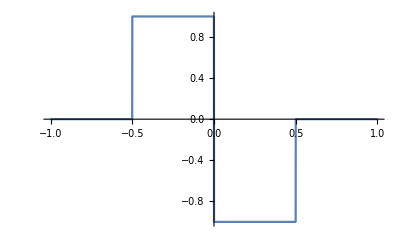

```mathematica
Plot[fr[t],{t,-1,1},Exclusions->None]
```

```mathematica
Subscript[cfr, n_]=Piecewise[{{∫_(-1/2)^(1/2) fr[t] ⅇ^(-2 π n ⅈ t)ⅆt, n≠ 0}, {0, n==0}}]
```

Piecewise[{{-(ⅈ (-1+(-1)^n))/(n π), n≠0}, {0, True}}]

Note: we have to set the coefficient n=0 explicitly to zero, since the calculation of this coefficients returns indeterminate.

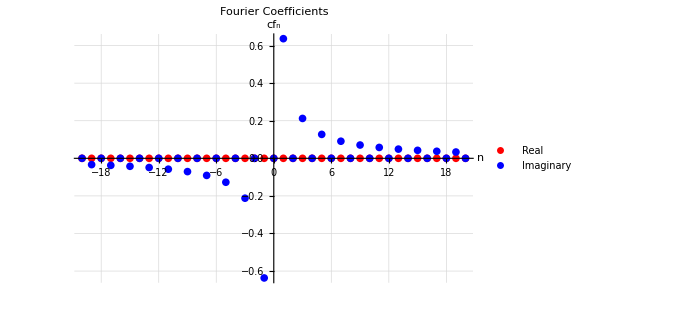

```mathematica
ListPlot[{Table[{n,Re[Subscript[cfr, n]]},{n,-20,20}],Table[{n,Im[Subscript[cfr, n]]},{n,-20,20}]},PlotRange->Full,GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"n","cf_n"},PlotStyle->{Red,Blue},BaseStyle->12,PlotLabel->"Fourier Coefficients",PlotLegends->{"Real","Imaginary"}]
```

Reconstruct the time-series using the number of coefficients to reconstruct the time-series as a parameter that can be adjusted.

```mathematica
frr[t_,m_]=∑_(n=-m)^m Subscript[cfr, n] ⅇ^(2 π n ⅈ t)
```

(Piecewise[{{-(2 ⅈ ⅇ^(-2 ⅈ π t))/π, m==1}, {1/((1+m) π)ⅈ ⅇ^(-2 ⅈ (1+m) π t) ((-1)^m Hypergeometric2F1[1,1+m,2+m,-ⅇ^(-2 ⅈ π t)]+Hypergeometric2F1[1,1+m,2+m,ⅇ^(-2 ⅈ π t)]+ⅇ^(2 ⅈ (1+m) π t) Log[ⅇ^(-2 ⅈ π t) (-1+ⅇ^(2 ⅈ π t))]+ⅇ^(2 ⅈ (1+m) π t) m Log[ⅇ^(-2 ⅈ π t) (-1+ⅇ^(2 ⅈ π t))]-ⅇ^(2 ⅈ (1+m) π t) Log[ⅇ^(-2 ⅈ π t) (1+ⅇ^(2 ⅈ π t))]-ⅇ^(2 ⅈ (1+m) π t) m Log[ⅇ^(-2 ⅈ π t) (1+ⅇ^(2 ⅈ π t))]), m>1}, {0, True}}])+(Piecewise[{{(2 ⅈ ⅇ^(2 ⅈ π t))/π, m==1}, {-1/((1+m) π)ⅈ ((-1)^m ⅇ^(2 ⅈ (1+m) π t) Hypergeometric2F1[1,1+m,2+m,-ⅇ^(2 ⅈ π t)]+ⅇ^(2 ⅈ (1+m) π t) LerchPhi[ⅇ^(2 ⅈ π t),1,1+m]+ⅇ^(2 ⅈ (1+m) π t) m LerchPhi[ⅇ^(2 ⅈ π t),1,1+m]+Log[1-ⅇ^(2 ⅈ π t)]+m Log[1-ⅇ^(2 ⅈ π t)]-Log[1+ⅇ^(2 ⅈ π t)]-m Log[1+ⅇ^(2 ⅈ π t)]), m>1}, {0, True}}])

Plot the reconstructed signal with the number of terms as a parameter to be set independently:

```mathematica
Manipulate[Plot[{Re[frr[t,m]],Im[frr[t,m]]},{t,-1/2,1/2},PlotRange->Full,GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"t","t(t)"},PlotStyle->{Red,Blue},BaseStyle->12,PlotLabel->StringForm["m=`1`",m]],{{m,1},0,50,1}]
```

Signals: Continuous and Discrete

## Discrete-time systems

Time Series

## From Continuous-time to Discrete-time

### Intro

Making table at equal time intervals

### Time-Series construction

Constructing a time series is not difficult, From the analytical description of a time function, you pick the values at regular intervals, using the Table function.

#### Example: sine function

The analytical expression

```mathematica
ts1[t_]=Sin[(2 π t)/4];
```

Plot the function

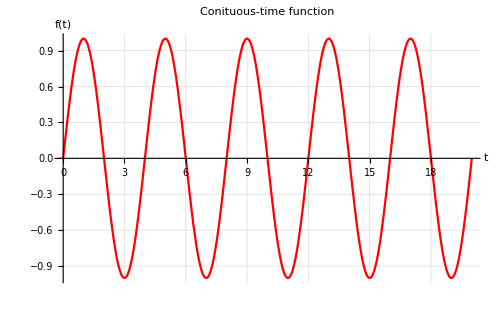

```mathematica
plt1=Plot[ts1[t],{t,0,20},PlotStyle->Red,PlotRange->Full,GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"t","f(t)"},BaseStyle->12,PlotLabel->"Conituous-time function"]
```

Define a time interval for sampling the Sine function

```mathematica
Δt=0.15
```

0.15

```mathematica
ts1n=Table[ts1[n Δt],{n,1,20/Δt}];
```

```mathematica
ts1n2=TimeSeries[Table[{n Δt,ts1[n Δt]},{n,1,20/Δt}]];
```

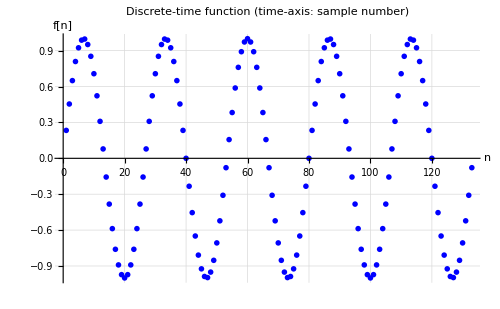

```mathematica
plt2=ListPlot[ts1n,PlotMarkers->o,PlotStyle->Blue,PlotRange->Full,GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"n","f[n]"},BaseStyle->12,PlotLabel->"Discrete-time function (time-axis: sample number)"]
```

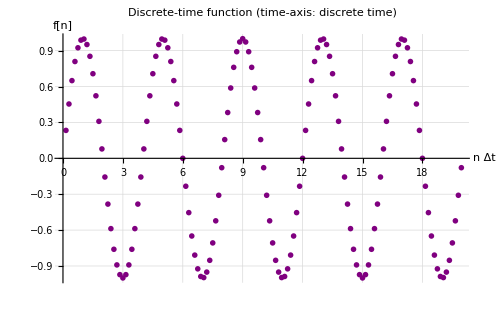

```mathematica
plt3=ListPlot[ts1n2,PlotMarkers->Δ,PlotStyle->Purple,PlotRange->Full,GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"n Δt","f[n]"},BaseStyle->12,PlotLabel->"Discrete-time function (time-axis: discrete time)"]
```

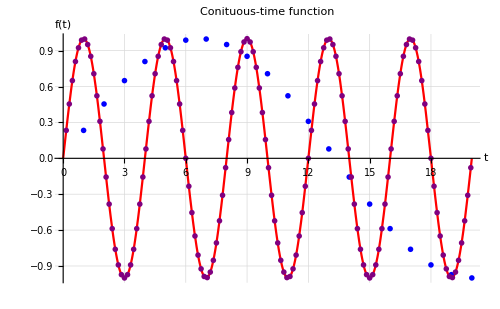

```mathematica
Show[{plt1,plt2,plt3}]
```

Fourier Transform Discrete

### Intro

Like with the FourierTransform, also with the the Fourier function for discrete transforms, we have to use the FourierParamters → {1,-1} as the extra option in the function to be consistent with  the Fourier definition in this course (Signal Processing standard).

### The function Fourier for a discrete Fourier Transform of a series of data

Below you find an animation of the Discrete Fourier Transform of a data set that consists of a repetitive {1,0,-1,0} sequency. Both the Time-Series as well as the Fourier Coefficients are plotted in separate graphs. Note that in case the number of samples is not equal to a multiple of four, the length of one period, the frequency spectrum does not spike at one frequency. This illustrates the effect of frequency leakage.

```mathematica
Manipulate[Grid[{{ListPlot[Re[Table[Re[ⅇ^(ⅈ π/2 i)],{i,0,nn}]],PlotRange->Full, Filling->Axis,PlotMarkers->{ "o"},PlotStyle->{Red,Blue},GridLines->Automatic,ImageSize->Large,AxesLabel->{"n","f[n]"},BaseStyle->14,PlotLabel->StringForm["Time Series of `1` samples of a repetative {1,0,-1,0} sequence",nn+1]]},{ListPlot[{Re[Fourier[Table[Re[ⅇ^(ⅈ π/2 i)],{i,0,nn}]]],Im[Fourier[Table[Re[ⅇ^(ⅈ π/2 i)],{i,0,nn}]]]},PlotRange->{-5.5,5.5}, Filling->Axis,PlotMarkers->{ "o", "o"},PlotStyle->{Red,Blue},GridLines->Automatic,ImageSize->Large,PlotLegends->{"Real coef","Imaginary coef"},AxesLabel->{"n","cf[n]"},BaseStyle->14,PlotLabel->StringForm["DFT of `1` samples of a repetative {1,0,-1,0} sequence",nn+1]]}},Alignment->{{Left},{Left}}],{nn,4,100,1}]
```

### Calculate the Fourier Transform of two series

First we construct a signal that consists of two pure harmonics. We chose two representations of the signal, differing in the number of samples.

```mathematica
Subscript[ν, 1]=3; Subscript[ν, 2]=5; n=12; fs=300;
```

```mathematica
nn=3/2 2^n
```

6144

```mathematica
nm=2^n
```

4096

```mathematica
x1=Table[Sin[i 2 π Subscript[ν, 1]/fs]+Sin[i 2 π Subscript[ν, 2]/fs] ,{i,0,nn}];
```

```mathematica
tx1=Table[{(i/fs).Sin[i 2 π Subscript[ν, 1]/fs]+Sin[i 2 π Subscript[ν, 2]/fs] },{i,0,nn}];
```

```mathematica
x2=Table[Sin[i 2 π Subscript[ν, 1]/fs]+Sin[i 2 π Subscript[ν, 2]/fs] ,{i,0,nm}];
```

```mathematica
tx2=Table[{i/fs,Sin[i 2 π Subscript[ν, 1]/fs]+Sin[i 2 π Subscript[ν, 2]/fs]} ,{i,0,nm}];
```

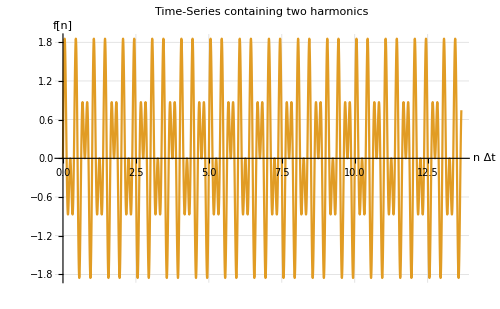

```mathematica
ListLinePlot[{tx1,tx2},PlotRange->Full,GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"n Δt","f[n]"},BaseStyle->12,PlotLabel->"Time-Series containing two harmonics"]
```

```mathematica
ts1=nn/fs
```

512/25

```mathematica
ts2=nm/fs
```

1024/75

```mathematica
fx1=2 Abs[Fourier[x1]];
```

```mathematica
fx2=2 Abs[Fourier[x2]];
```

```mathematica
wxfx1=Table[{i/ts1,fx1[[i]]},{i,0, nn/2+1}];
```

```mathematica
wxfx2=Table[{i/ts2,fx2[[i]]},{i,0, nm/2+1}];
```

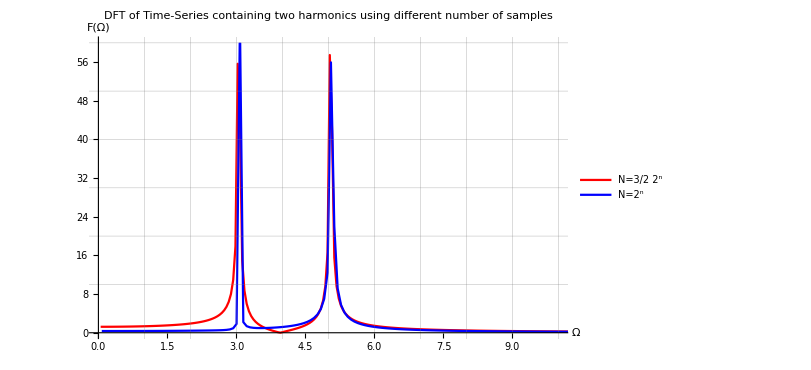

```mathematica
ListLinePlot[{wxfx1,wxfx2},PlotRange->{{0,10},{0,60}},PlotStyle->{Red,Blue},GridLines->{{1,2,3,4,5,6,7,8,9,10}, {10,20,30,40,50,60}},AxesLabel->{"Ω","F(Ω)"},BaseStyle->12,PlotLabel->"DFT of Time-Series containing two harmonics using different number of samples",PlotLegends->{"N=3/2 2^n","N=2^n"},ImageSize-> 600]
```

```mathematica
time=3/2 2^n
```

6144

```mathematica
1/time 30
```

5/1024

## FourierSequenceTransform

The function FourierSequenceTransform is used in case a discrete-time function is defined as a function of a time index number.

### Problem 21.1

```mathematica
x1[n_]=Sin[(2 π a n)/nn]
```

Set::write: Tag List in {0,Sin[π/50]+Sin[π/30],Sin[π/25]+Sin[π/15],1/4 (-1+√5)+Sin[(3 π)/50],Sin[(2 π)/25]+Sin[(2 π)/15],1/2+1/4 (-1+√5),√(5/8-(√5)/8)+Sin[(3 π)/25],Sin[(7 π)/50]+Sin[(7 π)/30],Cos[(7 π)/30]+Sin[(4 π)/25],«33»,-√(5/8+(√5)/8)+Sin[(4 π)/25],-Cos[π/15]+Sin[(7 π)/50],-Cos[π/30]+Sin[(3 π)/25],-1+1/4 (-1+√5),-Cos[π/30]+Sin[(2 π)/25],-Cos[π/15]+Sin[(3 π)/50],-√(5/8+(√5)/8)+Sin[π/25],-Cos[(2 π)/15]+Sin[π/50],«6095»}[n_] is Protected.

Sin[(a π)/256]

```mathematica
FourierSequenceTransform[x1[n],n,Ω]
```

Context::ssle: Symbol, string, or HoldPattern[symbol] expected at position 1 in Context[{0,Sin[π/50]+Sin[π/30],Sin[π/25]+Sin[π/15],1/4 (-1+√5)+Sin[(3 π)/50],Sin[(2 π)/25]+Sin[(2 π)/15],1/2+1/4 (-1+√5),√(5/8-(√5)/8)+Sin[(3 π)/25],Sin[(7 π)/50]+Sin[(7 π)/30],Cos[(7 π)/30]+Sin[(4 π)/25],«34»,-Cos[π/15]+Sin[(7 π)/50],-Cos[π/30]+Sin[(3 π)/25],-1+1/4 (-1+√5),-Cos[π/30]+Sin[(2 π)/25],-Cos[π/15]+Sin[(3 π)/50],-√(5/8+1/8 Power[«2»])+Sin[π/25],-Cos[(2 π)/15]+Sin[π/50],«6095»}].

DownValues::sym: Argument {0,Sin[π/50]+Sin[π/30],Sin[π/25]+Sin[π/15],1/4 (-1+√5)+Sin[(3 π)/50],Sin[(2 π)/25]+Sin[(2 π)/15],1/2+1/4 (-1+√5),√(5/8-(√5)/8)+Sin[(3 π)/25],Sin[(7 π)/50]+Sin[(7 π)/30],Cos[(7 π)/30]+Sin[(4 π)/25],«33»,-√(5/8+(√5)/8)+Sin[(4 π)/25],-Cos[π/15]+Sin[(7 π)/50],-Cos[π/30]+Sin[(3 π)/25],-1+1/4 (-1+√5),-Cos[π/30]+Sin[(2 π)/25],-Cos[π/15]+Sin[(3 π)/50],-√(5/8+(√5)/8)+Sin[π/25],-Cos[(2 π)/15]+Sin[π/50],«6095»} at position 1 is expected to be a symbol.

FourierSequenceTransform[{0,Sin[π/50]+Sin[π/30],Sin[π/25]+Sin[π/15],1/4 (-1+√5)+Sin[(3 π)/50],Sin[(2 π)/25]+Sin[(2 π)/15],1/2+1/4 (-1+√5),√(5/8-(√5)/8)+Sin[(3 π)/25],6132,Cos[(2 π)/15]+Sin[(11 π)/50],(√3)/2+√(5/8-(√5)/8),1/4 (1+√5)+Sin[(9 π)/50],Cos[(7 π)/30]+Sin[(4 π)/25],Sin[(7 π)/50]+Sin[(7 π)/30],√(5/8-(√5)/8)+Sin[(3 π)/25]}[12],12,Ω]
 |  |  |  |

```mathematica
x2[n_]=Cos[(2 π a n)/nn]
```

Set::write: Tag List in {0,Sin[π/50]+Sin[π/30],Sin[π/25]+Sin[π/15],1/4 (-1+√5)+Sin[(3 π)/50],Sin[(2 π)/25]+Sin[(2 π)/15],1/2+1/4 (-1+√5),√(5/8-(√5)/8)+Sin[(3 π)/25],Sin[(7 π)/50]+Sin[(7 π)/30],Cos[(7 π)/30]+Sin[(4 π)/25],«33»,-√(5/8+(√5)/8)+Sin[(4 π)/25],-Cos[π/15]+Sin[(7 π)/50],-Cos[π/30]+Sin[(3 π)/25],-1+1/4 (-1+√5),-Cos[π/30]+Sin[(2 π)/25],-Cos[π/15]+Sin[(3 π)/50],-√(5/8+(√5)/8)+Sin[π/25],-Cos[(2 π)/15]+Sin[π/50],«4047»}[n_] is Protected.

Cos[(a π)/256]

```mathematica
FourierSequenceTransform[x2[n],n,Ω]
```

Context::ssle: Symbol, string, or HoldPattern[symbol] expected at position 1 in Context[{0,Sin[π/50]+Sin[π/30],Sin[π/25]+Sin[π/15],1/4 (-1+√5)+Sin[(3 π)/50],Sin[(2 π)/25]+Sin[(2 π)/15],1/2+1/4 (-1+√5),√(5/8-(√5)/8)+Sin[(3 π)/25],Sin[(7 π)/50]+Sin[(7 π)/30],Cos[(7 π)/30]+Sin[(4 π)/25],«34»,-Cos[π/15]+Sin[(7 π)/50],-Cos[π/30]+Sin[(3 π)/25],-1+1/4 (-1+√5),-Cos[π/30]+Sin[(2 π)/25],-Cos[π/15]+Sin[(3 π)/50],-√(5/8+1/8 Power[«2»])+Sin[π/25],-Cos[(2 π)/15]+Sin[π/50],«4047»}].

DownValues::sym: Argument {0,Sin[π/50]+Sin[π/30],Sin[π/25]+Sin[π/15],1/4 (-1+√5)+Sin[(3 π)/50],Sin[(2 π)/25]+Sin[(2 π)/15],1/2+1/4 (-1+√5),√(5/8-(√5)/8)+Sin[(3 π)/25],Sin[(7 π)/50]+Sin[(7 π)/30],Cos[(7 π)/30]+Sin[(4 π)/25],«33»,-√(5/8+(√5)/8)+Sin[(4 π)/25],-Cos[π/15]+Sin[(7 π)/50],-Cos[π/30]+Sin[(3 π)/25],-1+1/4 (-1+√5),-Cos[π/30]+Sin[(2 π)/25],-Cos[π/15]+Sin[(3 π)/50],-√(5/8+(√5)/8)+Sin[π/25],-Cos[(2 π)/15]+Sin[π/50],«4047»} at position 1 is expected to be a symbol.

FourierSequenceTransform[{0,Sin[π/50]+Sin[π/30],Sin[π/25]+Sin[π/15],1/4 (-1+√5)+Sin[(3 π)/50],Sin[(2 π)/25]+Sin[(2 π)/15],1/2+1/4 (-1+√5),√(5/8-(√5)/8)+Sin[(3 π)/25],4083,(√3)/2-√(5/8-(√5)/8),Cos[(2 π)/15]-Sin[(9 π)/50],√(5/8+(√5)/8)-Sin[(4 π)/25],Cos[π/15]-Sin[(7 π)/50],Cos[π/30]-Sin[(3 π)/25],1+1/4 (1-√5),Cos[π/30]-Sin[(2 π)/25]}[12],12,Ω]
 |  |  |  |

#### Problem 21.3

```mathematica
x3[n_]=(Cos[2 π f0 t]/.t->n/fs)/.f0/fs->k0/nn
```

Cos[(2 f0 π)/25]

### Other signal

```mathematica
paramo={a->3/4}
```

{a→3/4}

```mathematica
fx3[Ω_]=FourierSequenceTransform[x3[n],n,Ω]
```

2 π Cos[(2 f0 π)/25] DiracDelta[Ω]

```mathematica
fst[Ω_]=FourierSequenceTransform[a^n UnitStep[n] ,n,Ω]
```

FourierSequenceTransform[a^12,12,Ω]

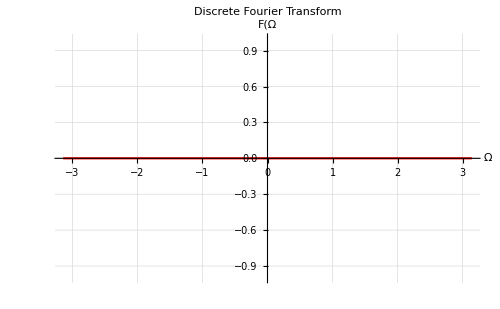

```mathematica
Plot[{Re[fst[Ω]]/.paramo,Im[fst[ω]]/.paramo},{Ω,-π,π},PlotStyle->Red,PlotRange->Full,GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"Ω","F(Ω"},BaseStyle->12,PlotLabel->"Discrete Fourier Transform"]
```

## Calculate a few Fourier Transform Pairs from the table

#### Exponent

```mathematica
FourierSequenceTransform[ⅇ^(ⅈ (2 π kd1 nd)/nn),nd,kd]
```

6144 π DiracDelta[3072 kd-kd1 π]

#### Sine

```mathematica
FourierSequenceTransform[Sin[(2 π kd1 nd)/nn],nd,kd]
```

-ⅈ π (3072 DiracDelta[3072 kd-kd1 π]-3072 DiracDelta[3072 kd+kd1 π])

#### Cosine

```mathematica
FourierSequenceTransform[Cos[(2 π kd1 nd)/nn],nd,kd]
```

π (3072 DiracDelta[3072 kd-kd1 π]+3072 DiracDelta[3072 kd+kd1 π])

#### DC-signal

```mathematica
FourierSequenceTransform[1,nd,kd]
```

2 π DiracDelta[kd]

#### Finite Pulse

```mathematica
FourierSequenceTransform[UnitStep[nd+nd1]-UnitStep[nd-nd1],nd,kd]//FullSimplify
```

Piecewise[{{-1-ⅇ^(ⅈ kd), nd1==-1}, {(ⅇ^(-ⅈ kd (-1+nd1)) (-1+ⅇ^(2 ⅈ kd nd1)))/(-1+ⅇ^(ⅈ kd)), True}}]

```mathematica
ExpToTrig[%]
```

Piecewise[{{-1-ⅇ^(ⅈ kd), nd1==-1}, {(ⅇ^(-ⅈ kd (-1+nd1)) (-1+ⅇ^(2 ⅈ kd nd1)))/(-1+ⅇ^(ⅈ kd)), True}}]

#### Exponential decay

```mathematica
FourierSequenceTransform[a^nd UnitStep[nd],nd,kd]
```

ⅇ^(ⅈ kd)/(-a+ⅇ^(ⅈ kd))

#### 1-Exponential decay

```mathematica
FourierSequenceTransform[(1-a^nd) UnitStep[nd],nd,kd]
```

-((-1+a) ⅇ^(ⅈ kd))/((-1+ⅇ^(ⅈ kd)) (-a+ⅇ^(ⅈ kd)))

```mathematica
%//FullSimplify
```

a/(a-ⅇ^(ⅈ kd))+1/(-1+ⅇ^(ⅈ kd))

#### Lorentzian shaped time series

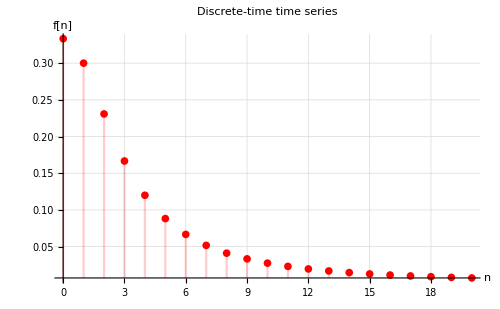

```mathematica
DiscretePlot[nd1/(nd1^2+nd^2)/.nd1->3,{nd,0,20},PlotStyle->Red,PlotRange->Full,GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"n","f[n]"},BaseStyle->14,PlotLabel->"Discrete-time time series"]
```

```mathematica
FourierSequenceTransform[nd1/(nd1^2+nd^2),nd,kd]//FullSimplify
```

1/(2 (nd1+nd1^3))(ⅇ^(ⅈ kd) nd1 (-ⅈ+nd1) Hypergeometric2F1[1,1-ⅈ nd1,2-ⅈ nd1,ⅇ^(ⅈ kd)]+ⅇ^(ⅈ kd) nd1 (ⅈ+nd1) Hypergeometric2F1[1,1+ⅈ nd1,2+ⅈ nd1,ⅇ^(ⅈ kd)]+(1+nd1^2) (Hypergeometric2F1[1,-ⅈ nd1,1-ⅈ nd1,ⅇ^(-ⅈ kd)]+Hypergeometric2F1[1,ⅈ nd1,1+ⅈ nd1,ⅇ^(-ⅈ kd)]))

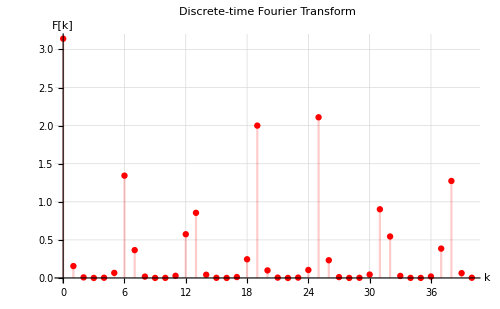

```mathematica
DiscretePlot[Re[FourierSequenceTransform[nd1/(nd1^2+nd^2),nd,kd]/.nd1->3],{kd,0,40},PlotStyle->Red,PlotRange->Full,GridLines->Automatic,GridLinesStyle->Dotted,ImageSize->500,AxesLabel->{"k","F[k]"},BaseStyle->14,PlotLabel->"Discrete-time Fourier Transform"]
```